Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 8: Funciones de varias variables II (Derivadas, Extremos, Integrales). Notas y prácticas

## Funciones de varias variables.

## Introducción Derivadas parciales Plano tangente a la gráfica de una función de dos variables Aproximación de una función por el plano tangente Estimación de errores

Muchas gráficas de funciones de dos variables tienen plano tangente en cada punto de la gráfica. Para ello las derivadas direccionales deberían estar “coordinadas”, y todas las rectas tangentes a la gráfica deberían estar incluidas en un plano, el plano tangente. Cuando la función es diferenciable, las derivadas parciales condicionan al resto de derivadas direccionales y esto permite que haya plano tangente a la gráfica de la función. La definición de de función diferenciable es compleja, sin embargo basta que una función tenga derivadas parciales continuas para que la función sea diferenciable y tengamos plano tangente.

Consideremos la función f(x,y)

```mathematica
Limit[f[t Cos[s],t Sin[s]]/t,t->0]
```

Cos[s]^3/(Cos[s]^2+Sin[s]^2)

```mathematica
f[x_,y_]:=x^3/(x^2+y^2)
```

```mathematica
g[x_,y_]:=-(2 x^4)/((x^2+y^2)^2)+(3 x^2)/(x^2+y^2)
```

```mathematica
Limit[g[x,y]/.y->0,x->0]
```

1

```mathematica
D[x^3/(x^2+y^2),y]
```

-(2 x^3 y)/((x^2+y^2)^2)

```mathematica
D[x^3/(x^2+y^2),y]
```

-(2 x^3 y)/((x^2+y^2)^2)

```mathematica
recta1=ParametricPlot3D[{{t,0,t},{0,t,0},t*{Cos[Pi/4],Cos[Pi/4],Cos[Pi/4]^3}},{t,-2,2}]
```

-Graphics3D-

```mathematica
graf=Plot3D[{(x^3)/(x^2+y^2)},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Show[graf,recta1]
```

-Graphics3D-

Plano tangente a la gráfica de f(x, y) en el punto (x0, y0).
Cuando la función es diferenciable, tenemos garantizada la existencia de plano tangente.
La fórmula es similar a la de la recta tangente (recordemos y=f(x0)+f ‘(x0)(x-x0) ) añadiendo un nuevo sumando al haber dos derivadas parciales.
			z=f(x0,y0) + ∂_x f(x0,y0) (x-x0)+∂_y f(x0,y0) (y-y0)
-Graphics3D-
El vector formado por las derivadas parciales, (∂_x f(x0,y0), ∂_y g(x0,y0)), se llama vector gradiente. El vector gradiente marca la dirección de máxima pendiente y es perpendicular a las curvas de nivel.

Cuando la función es diferenciable, las derivadas direccionales pueden calcularse haciendo el producto escalar del vector v por el vector gradiente:
			D_(v1,v2)f(x0,y0) = v1*(∂f)/(∂x)(x0,y0) + v2*(∂f)/(∂y)(x0,y0)

-Graphics3D-
El plano tangente, cerca del punto de tangencia, puede ser una buena aproximación de la función y puede ser más fácil evaluar el plano (un polinomio) que la función.

Por ejemplo, si f(x,y)=e^(x+2y), el plano tangente en el punto (0,0) es
		z=f(0,0) + ∂_x f(0,0) (x-0)+∂_y f(0,0) (y-0) = 1+1*x+2*y = 1+x+2y
Así f(x,y)≃1+x+2y alrededor del (0,0).

Por ejemplo, f(0.1,0.1) = e^(0.1+2*0.1) = e^0.2 = 1.34986... mientras que el plano tangente vale 1+0.1+2*0.1=1.3.

Estimación de errores
En la práctica, los datos experimentales están sometidos a errores y las funciones que evaluamos con esos datos tendrán errores. Una forma de estimar los errores que los datos pueden inducir en una función es usar el plano tangente y tener una estimación del error. 
	Error en la función f = |f(x,y)-f(x0,y0)| ≃ |∂_x f(x0,y0)| * (error en la x) + |∂_y f(x0,y0)|* (error en la y).

Con el error que puede haber en las variables x e y, los multiplicamos por las derivadas parciales en el punto medido y sumamos para obtener una estimación del error máximo que podríamos tener en la función.

Cálculo de extremos relativos.
En una variable utilizábamos la derivada para calcular los extremos relativos (máximos y mínimos) de una función. La idea era que si una función derivable tenía un máximo relativo (o un mínimo relativo) en un punto interior al dominio, su derivada debía ser cero. 
En dos variables, si una función tiene un máximo o mínimo relativo en (x0,y0), punto interior del dominio, tendremos que será máximo o mínimo relativo en los puntos de la forma (x,y0) ó (x0,y), por tanto las derivadas parciales serán cero. 
Así, cuando queramos buscar extremos relativos resolveremos el sistema
		∂_x f(x,y) = 0
		∂_y f(x,y) = 0
Las soluciones del sistema nos pueden llevar a los máximos y mínimos relativos.

Nos obstante, aparecen nuevas situaciones. Así, la función f(x,y) =  x^2 - y^2, en los puntos (x,0), f(x,0) = x^2 y tendrá un mínimo en el (0,0), en cambio en los puntos (0,y), f(0,y) =  - y^2, con lo que en el (0,0) habría un máximo en esta dirección. Diremos que f(x,y) tiene un punto de silla en el (0,0).

Para saber si un punto donde se anulan las derivadas es máximo, mínimo o punto de silla, recurrimos a las derivadas segundas. La situación es similar a lo que ocurre en una variable (si la derivada segunda era positiva había un mínimo, si la derivada segunda era negativa había un máximo y si la derivada segunda era cero, aparecía un caso de duda). 

Ahora hay cuatro derivadas segundas:
		(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y)) es la matriz hessiana
El determinante de esta matriz es el hessiano:
		|∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y)|
Si al resolver el sistema
		∂_x f(x,y) = 0
		∂_y f(x,y) = 0
nos encontramos con un punto (x0,y0) donde se anulan las primeras derivadas parciales, pasamos a calcular el Hessiano en ese punto
				Hessiano(x0,y0)=|∂_(x,x) f(x0,y0) | ∂_(x,y) f(x0,y0)
∂_(x,y) f(x0,y0) | ∂_(y,y) f(x0,y0)|.
* Si el Hessiano en ese punto es negativo, tendremos un punto de silla. 
* Si el Hessiano es positivo, habrá un máximo o un mínimo. Para saber si es máximo o mínimo, debemos estudiar la derivada segunda (en la x o la y, da igual). Si la derivada segunda ∂_(x,x) f(x0,y0) es mayor que cero, habrá un mínimo, si la derivada segunda fuese negativa, tendríamos un máximo.
* Si el Hessiano es cero, tendríamos un caso de duda y deberíamos estudiarlo por otros métodos.

Cálculo de máximos y mínimos absolutos
Como ocurría en una variable, en ocasiones nos interesa conocer, si existen, los máximos y mínimos absolutos. En muchas ocasiones, los máximos o mínimos absolutos no existen. El Teorema de Weierstrass nos garantiza, bajo unas hipótesis sencillas, que existe máximo y mínimo absolutos. En concreto, dice que si una función es continua en un conjunto cerrado y acotado, alcanza su máximo y mínimo absolutos.

En una variable, cuando teníamos una función continua en un intervalo [a,b], teníamos garantizada la existencia de máximo y mínimo absolutos. Para encontrarlos, considerábamos los puntos extremos y los puntos del interior. En el interior, considerábamos los puntos con derivada cero y los puntos sin derivada. Con todos los puntos encontrados, evaluamos la función en esos puntos y encontramos dónde esta el máximo y el mínimo de la función.

En varias variables, si tenemos una función continua en un conjunto cerrado y acotado, tendremos máximo y mínimo absolutos, que podrán estar en el borde o en el interior. Cuando la función es derivable, los puntos candidatos del interior serán los que tengan primera derivada cero. El problema aparece en el borde, pues no son solo dos puntos como en los intervalos de una variable, ahora aparecen infinitos.
En ocasiones podremos despejar una variable en función de la otra y dejar la función en una única variable. Otras veces, podremos expresar los puntos del borde en términos de un parámetro y llegar a una función de una variable. Otra opción es la técnica de los Multiplicadores de Lagrange.

Supongamos que los puntos del borde son los que cumplen g(x,y)=0. Para calcular los máximos y mínimos absolutos de f(x,y) con la condición g(x,y)=0, construimos la función:
		F(x,y,t) = f(x,y) + t g(x,y) 
y buscamos las soluciones del sistema
		∂_x F(x,y,t) = 0
		∂_y F(x,y,t) = 0
		∂_t F(x,y,t) = 0
Los valores solución de x e y, serán candidatos a máximos y mínimos.
Observemos que la condición ∂_t F(x,y,t) =0 es equivalente a g(x,y)=0.

## Derivadas

Como vimos al estudiar las funciones de una variable, la derivada es una herramienta para estudiar el cambio de una función.

Derivada direccional.
Tomando un vector unitario, v=(v1,v2), con módulo o longitud 1 (puede escribirse también de la forma (cos θ, sen θ) ), podemos estudiar el cambio en un punto (x0,y0) en la dirección v comparando f((x0,y0)+t(v1,v2)) con f(x0,y0)

		(f((x0,y0)+t(v1,v2))-f(x0,y0))/t

Si existe el límite cuando t tiende a 0, diremos que existe la derivada de f en la dirección v, D_v f(x0,y0).

		lim_(t→0) (f((x0,y0)+t(v1,v2))-f(x0,y0))/t=D_(v1,v2)f(x0,y0)
Si el vector v es (1,0) hablamos de la derivada parcial respecto a la primera variable:

	lim_(t→0) (f(x0+t,y0)-f(x0,y0))/t=D_(1,0)f(x0,y0)=(∂f)/(∂x)(x0,y0)

Análogamente, con el vector (0,1), llegaríamos a la derivada parcial respecto a la segunda variable:

	lim_(t→0) (f(x0,y0+t)-f(x0,y0))/t=D_(0,1)f(x0,y0)=(∂f)/(∂y)(x0,y0)

Habitualmente, para calcular las derivadas parciales no es necesario calcular estos límites. Basta recordar las reglas y propiedades de derivación en una variable.

Así, si f(x,y)=3 x^2 y+ 2 y^3+xy+ 4y+ 6, 
		(∂f)/(∂x)=6xy + y,
		(∂f)/(∂y)=3 x^2+ 6 y^2+x+ 4
Podríamos volver a derivar estas derivadas parciales,
	(∂((∂f)/(∂x)))/(∂x)=(∂^2 f)/(∂x)^2=6y, (∂((∂f)/(∂x)))/(∂y)=(∂^2 f)/(∂y∂x)=6x+1, (∂((∂f)/(∂y)))/(∂x)=(∂^2 f)/(∂x∂y)=6x+1, (∂((∂f)/(∂y)))/(∂y)=(∂^2 f)/(∂y)^2=12y

Observamos que las derivadas parciales, (∂^2 f)/(∂y∂x) y (∂^2 f)/(∂x∂y) son iguales. Esto es lo habitual. Puede demostrarse que si las derivadas parciales existen y son continuas, el orden de derivación no importa. El Mathematica solo pide cuántas veces hay que derivar respecto a cada variable, sin pedir el orden de derivación.
Para calcular las derivadas de una función de varias variables podemos usar la instrucción D y también la paleta.

```mathematica
f[x_,y_,z_]:= 3x^2 y + Cos[y*z]+Sin[x]*y^2
```

```mathematica
g[x_,y_]:= x^2+y^2
```

La derivada direccional de la función g en el punto (2,1) en la dirección (cos (π/6), sen (π/6)) es:

```mathematica
Limit[(g[2+t Cos[Pi/6],1+t Sin[Pi/6]]-g[2,1])/t,t->0]
```

1/4 (4+8 √3)

La derivada direccional de la función g en el punto (x,y) en la dirección (1, 0) es:

```mathematica
Limit[(g[x+t ,y]-g[x,y])/t,t->0]
```

2 x

La derivada direccional en la dirección (1,0) es la derivada parcial en la variable x:

```mathematica
D[g[x,y],x]
```

2 x

```mathematica
Limit[(g[x+t Cos[s],y+t Sin[s]]-g[x,y])/t,t->0]
```

2 x Cos[s]+2 y Sin[s]

```mathematica
Limit[(g[x+t Cos[s],y+t Sin[s]]-g[x,y])/t,t->0]
```

2 x Cos[s]+2 y Sin[s]

La derivada direccional de la función g en el punto (x,y) en la dirección (cos s, sen s) es 2x cos s + 2 y sen s. 
El gradiente de g(x,y) es (∂g)/(∂x)=2x, (∂g)/(∂y)=2y.

```mathematica
{D[g[x,y], x],D[g[x,y], y]}
```

{2 x,2 y}

La derivada direccional de la función g en el punto (x,y) en la dirección (cos s, sen s) es 2x cos s + 2 y sen s. 
El gradiente de g(x,y) es (∂g)/(∂x)=2x, (∂g)/(∂y)=2y.
Como g(x,y) es diferenciable, la derivada direccional de g(x,y) se puede calcular multiplicando el vector unitario de dirección por el vector gradiente.

```mathematica
Grad[g[x,y],{x,y}]
```

{2 x,2 y}

```mathematica
Grad[g[x,y],{x,y}].{Cos[s],Sin[s]}
```

2 x Cos[s]+2 y Sin[s]

```mathematica
{D[g[x,y], x],D[g[x,y], y]}
```

{2 x,2 y}

```mathematica
D[f[x,y,z],{x,1},{y,2}]
```

2 Cos[x]

```mathematica
D[g[x,y], x]
```

2 x

También podemos evaluar en un punto determinado.

```mathematica
D[f[x,y,z],{x,1},{y,2}]/.{x->1,y->2,z->-1}
```

2 Cos[1]

Observemos que el Mathematica no pregunta el orden para realizar las derivadas, simplemente pregunta cuántas veces en cada variable. Si las derivadas parciales existen y son continuas, entonces es independiente el orden de derivación.

Plano tangente a la gráfica de g[x, y] en el punto (1, 2).
La fórmula es similar a la de la recta tangente (recordemos y=f(x0)+f ’(x0)(x-x0) ) añadiendo un nuevo sumando al haber dos derivadas parciales.
z=g(1,2) + ∂_x g(1,2) (x-1)+∂_y g(1,2) (y-2)

```mathematica
g[x,y]
```

x^2+y^2

```mathematica
g[1,2]+(D[g[u,v],u]/.{u->1,v->2})(x-1)+ (D[g[u,v],v]/.{u->1,v->2} )(y-2)
```

5+2 (-1+x)+4 (-2+y)

```mathematica
Plot3D[{g[x,y],5+2 (-1+x)+4 (-2+y)},{x,-4,6},{y,-3,7}]
```

-Graphics3D-

Observemos que el Mathematica no pregunta el orden para realizar las derivadas, simplemente pregunta cuántas veces en cada variable. Si las derivadas parciales existen y son continuas, entonces es independiente el orden de derivación.


Plano tangente a la gráfica de g[x, y] en el punto (1, 2).
La fórmula es similar a la de la recta tangente (recordemos y=f(x0)+f ’(x0)(x-x0) ) añadiendo un nuevo sumando al haber dos derivadas parciales.
z=g(1,2) + ∂_x g(1,2) (x-1)+∂_y g(1,2) (y-2)

El vector gradiente en ese punto es el vector  (∂_x g(1,2) , ∂_y g(1,2)). Muestra la dirección de mayor crecimiento de la función g(x,y) en ese punto.

```mathematica
g[1,2]+(D[g[x,y],x]/.{x->1,y->2}) (x-1)+(D[g[x,y],y]/.{x->1,y->2}) (y-2)
```

5+2 (-1+x)+4 (-2+y)

El vector gradiente marca una dirección perpendicular a las curvas de nivel.

```mathematica
Show[ContourPlot[g[x,y]==g[1,2],{x,0,2},{y,1,3}],ParametricPlot[{1,2}+t{(D[g[x,y],x]/.{x->1,y->2}) ,(D[g[x,y],y]/.{x->1,y->2})},{t,-1,1}],ListPlot[{{1,2}}],AspectRatio->Automatic]
```

-Graphics-

Podemos dibujar la gráfica de la función y del plano tangente.

```mathematica
Plot3D[{g[x,y],5+2 (-1+x)+4 (-2+y)},{x,-2,4},{y,-2,4}]
```

-Graphics3D-

El plano tangente nos sirve también para estimar el valor de la función en puntos cercanos al punto de tangencia. Evaluemos la función y el plano tangente en el punto (0.95, 2.01)

```mathematica
g[0.95,2.01]
```

4.9426

```mathematica
5+2 (-1+x)+4 (-2+y)/.{x->0.95,y->2.01}
```

4.94

Estimación de errores
Supongamos que queremos conocer el área de un rectángulo. El área sería la función f(x,y)=xy donde x e y son las longitudes de los lados del rectángulo. Si medimos los lados y obtenemos x=20 y=40, el área será 20*40=800.
Si la cinta métrica con la que medimos tiene un margen de error de 0.5, cuál sería el error que podríamos tener en el área.

Con el plano tangente tendríamos que f(x,y) se aproximaría por f(20,40) + ∂_x f(20,40) (x-20)+∂_y f(20,40) (y-40)
como ∂_x f(x,y)=y, ∂_y f(x,y)=x, tenemos que ∂_x f(20,40)=40, ∂_y f(20,40)=20.
Si la diferencia entre el valor real x y el valor medido 20 es menor que 0.5, e igualmente para y, tenemos que el error
|f(x,y)-f(20,40)| se podría estimar por |∂_x f(20,40)| 0.5 + |∂_y f(20,40)| 0.5=40*0.5+20*0.5=20+10=30.
En este caso, al ser la parcial respecto de x mayor, el error en la x introduce un mayor error en la función.
El error en las mediciones podría traer como consecuencia que el valor calculado del área, 800, tenga un error estimado de hasta 30.

Esta estimación del error se podría mejorar utilizando también derivadas de orden superior.

Otro ejemplo:
El índice de masa corporal se define como el cociente entre el peso (medido en kilogramos) y la altura (medida en metros) elevada al cuadrado, I=M/H^2. 

Supongamos que la báscula nos da un peso de 80Kg. y que la cinta métrica nos da un valor de 1.7 m. Si la báscula tiene un margen de error de 1 kg y la cinta métrica un error de 2 cms, calcular el error que cada medida puede inducir en el índice de masa corporal. ¿Cuál puede inducir más error? o ¿qué aparato deberíamos cambiar antes?

```mathematica
F[M_,H_]:=M/H^2
```

```mathematica
F[80,1.7]
```

27.6817

```mathematica
1*D[F[M,H],M]/.{M->80,H->1.7}
```

0.346021

```mathematica
0.02*D[F[M, H], H] /. {M -> 80, H -> 1.7}
```

-0.651333

El índice de masa corporal calculado es 27.6817. La báscula puede introducir un error de 0.346021, mientras que la cinta métrica podría introducir un error de 0.651333. Por tanto, la cinta métrica induce un error mayor (sería lo más urgente en cambiar). La estimación del error debido a los datos erróneos puede llegar a 0.346021+0.651333=0.997354.

## Cálculo de máximos y de mínimos (y de puntos de silla). Extremos relativos

Al igual que con funciones de una variable, podemos preguntarnos por los máximos y mínimos de una función de varias variables.

Una posibilidad es buscar máximos o mínimos locales. Se trata de puntos donde la función es mayor o igual (o menor o igual) que en todos los de un entorno del punto. Como las funciones suelen ser derivables, la herramienta que se utiliza en este caso es la derivada. Los puntos interiores del dominio de una función derivable que sean máximos o mínimos locales, lo serán en cada una de las variables, por tanto tendrán todas las derivadas igual a cero. Por ello, derivamos y buscamos los posibles puntos.

Otra posibilidad es buscar máximos o mínimos absolutos en conjuntos cerrados y acotados. En esta situación, basta que la función sea continua para tener la seguridad de que existirán (Teorema de Weiertrass). Para encontrarlos, distinguimos los puntos del interior y el borde. En el interior estarían en puntos donde la derivada se anule, o en puntos donde la función no sea derivable.

Consideremos las funciones f1(x,y) = x^2+ y^2, f2(x,y) = x^2- y^2, f3(x,y) = -x^2- y^2, f4(x,y) = x^4+ y^4, y busquemos sus extremos relativos.

```mathematica
f1[x_,y_]:= x^2+ y^2
```

```mathematica
Solve[{D[f1[x,y],x]==0,D[f1[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f1[x,y], x,x], D[f1[x,y], x,y]}, {D[f1[x,y], x,y], D[f1[x,y], y,y]}})]/.{x->0,y->0}
```

4

Como el hessiano es mayor que cero, significa que habrá un máximo o un mínimo local. Para saber qué es, estudiamos el signo de la derivada segunda (en la x o en la y).

```mathematica
D[f1[x,y],{x,2}]/.{x->0,y->0}
```

2

Al ser positiva se trata de un mínimo.

```mathematica
f2[x_,y_]:= x^2- y^2
```

```mathematica
Solve[{D[f2[x,y],x]==0,D[f2[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f2[x,y], x,x], D[f2[x,y], x,y]}, {D[f2[x,y], x,y], D[f2[x,y], y,y]}})]/.{x->0,y->0}
```

-4

Como el hessiano es menor que cero, significa que habrá un punto de silla.

```mathematica
f3[x_,y_]:= -x^2- y^2
```

```mathematica
Solve[{D[f3[x,y],x]==0,D[f3[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f3[x,y], x,x], D[f3[x,y], x,y]}, {D[f3[x,y], x,y], D[f3[x,y], y,y]}})]/.{x->0,y->0}
```

4

Como el hessiano es mayor que cero, significa que habrá un máximo o un mínimo local. Para saber qué es estudiamos el signo de la derivada segunda (en la x o en la y).

```mathematica
D[f3[x,y],{x,2}]/.{x->0,y->0}
```

-2

Al ser negativa se trata de un máximo.

```mathematica
f4[x_,y_]:= x^4+ y^4
```

```mathematica
Solve[{D[f4[x,y],x]==0,D[f4[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f4[x,y], x,x], D[f4[x,y], x,y]}, {D[f4[x,y], x,y], D[f4[x,y], y,y]}})]/.{x->0,y->0}
```

0

Como el hessiano es cero, este criterio no nos da información.

Veamos las gráficas de las funciones estudiadas.

```mathematica
{Plot3D[f1[x,y],{x,-2,2},{y,-2,2}],Plot3D[f2[x,y],{x,-2,2},{y,-2,2}],Plot3D[f3[x,y],{x,-2,2},{y,-2,2}],Plot3D[f4[x,y],{x,-2,2},{y,-2,2}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

En el caso de f1 tenemos un mínimo, en el de f2 un punto de silla, en el de f3 un máximo y en el de f4 hay un mínimo, aunque el criterio no nos dio información. Si en lugar de f4, hubiésemos estudiado las funciones x^4- y^4 o -x^4- y^4, el criterio del hessiano no nos daría información, siendo el primer ejemplo un punto de silla y el segundo un máximo.

Este criterio es similar al que teníamos de la derivada segunda en funciones de una variable. Si la derivada segunda era mayor que cero había un mínimo, si era menor que cero había un máximo, pero si era cero no podíamos concluir nada.

Veamos otro ejemplo. Calcular los extremos de la función f(x,y).

```mathematica
f[x_,y_]:=y^3+x^2 y + 2 x^2 + 2 y^2-4y-8
```

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→-2},{x→0,y→2/3},{x→0,y→-2}}

Los puntos (0, -2) y (0, 2/3) son puntos críticos (Candidatos a ser máximos, mínimos o puntos de silla). Para evaluar el hessiano en diferentes puntos, definimos la función hessiano.

```mathematica
hess[x_,y_]:=Det[({{D[f[u,v], u,u], D[f[u,v], u,v]}, {D[f[u,v], u,v], D[f[u,v], v,v]}})]/.{u->x,v->y}
```

```mathematica
{hess[0,-2],hess[0,2/3]}
```

{0,128/3}

El hessiano en el (0,-2) es cero y no nos da información. En el punto (0,2/3) el hessiano es positivo y habrá máximo o mínimo. Para saberlo evaluamos la derivada segunda en la primera o la segunda variable.

```mathematica
D[f[u,v], u,u]/.{u->0,v->2/3}
```

16/3

La función en (0, 2/3) tiene un mínimo local. En el punto (0, -2) no sabemos con la prueba del Hessiano si tiene máximo, mínimo o punto de silla.

```mathematica
Plot3D[f[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

## Extremos absolutos (Multiplicadores de Lagrange)

Supongamos ahora el mismo problema con la condición de que x^2 + y^2 ≤ 1. En este caso el conjunto donde vamos a estudiar la función es cerrado y acotado, y al ser la función continua, tendremos máximos y mínimos absolutos. Estos podrán estar dentro o en el borde. 

1) Dentro: Para estudiar posibles máximos o mínimos dentro, y dado que la función es derivable, calculamos sus derivadas parciales e igualamos a cero.

```mathematica
Plot3D[Which[x^2+y^2≤1,f[x,y]],{x,-1,1},{y,-1,1},PlotPoints->100]
```

-Graphics3D-

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→-2},{x→0,y→2/3},{x→0,y→-2}}

El punto (0, -2) está fuera del disco (o no cumple la condición). Queda como candidato el punto (0,2/3).

2) Borde: También podría estar en la frontera, el borde del disco (cuando x^2 + y^2 = 1).

Para estudiar los máximos y mínimos en el borde, es decir, sujetos a esa condición, podemos utilizar la técnica de los multiplicadores de Lagrange. 

	2.1) Multiplicadores de Lagrange: Se trata de reunir en una misma función, la función f y la condición de estar en el borde.

```mathematica
F[x_,y_,t_]:= f[x,y]+t (x^2+y^2-1)
```

```mathematica
Solve[{D[F[x,y,t],x]==0,D[F[x,y,t],y]==0,D[F[x,y,t],t]==0},{x,y,t}]
```

{{x→0,y→-1,t→-5/2},{x→0,y→1,t→-3/2}}

Al hacer las derivadas parciales e igualar a cero, tenemos como puntos candidatos (0, 1), (0, -1).

Reuniendo todos los puntos candidatos tenemos (0,2/3), (0,1), (0,-1). Ahora evaluamos la función y vemos dónde vale más y dónde vale menos.

```mathematica
{f[0,2/3],f[0,1],f[0,-1]}//N
```

{-9.48148,-9.,-3.}

El máximo de la función se alcanza en el punto (0,-1) y es -3. El mínimo se alcanza en el punto (0,2/3) y vale -9.48.

	2.2) Otra forma: despejando
En algunos casos, en lugar de usar la técnica de los Multiplicadores de Lagrange, podríamos dejar la función en el borde con una sola variable. Para ello podríamos tratar de despejar x ó y, en función de la otra variable y sustituir en la función f.

Por ejemplo, en este caso x^2 + y^2 = 1, por tanto x^2 = 1 - y^2. Sustituyendo:
f(x,y)=y^3+x^2 y + 2 x^2 + 2 y^2-4y-8 =  y^3+(1-y^2) y + 2 (1-y^2) + 2 y^2-4y-8 = -3 (2+y) = g(y)

Obtenemos una función que depende ahora de una sola variable, y. En el borde, x^2 + y^2 = 1, la variable y se mueve en el intervalo [-1,1]. Por tanto, deberíamos buscar los máximos y mínimos de g(y) en el intervalo [-1,1]. Ahora tenemos un problema de máximos y mínimos absolutos en una variable. La función es continua en un intervalo cerrado y acotado. Como la derivada g’(y) =-3, no es cero, no tenemos candidatos del interior del intervalo. Al ser derivable sólo nos quedan como candidatos los extremos del intervalo, y=1, -1. Dado que x^2 + y^2 = 1, cuando y=1, x debe ser 0. Igualmente, si y=-1, x=0. Por tanto, los puntos candidatos que encontramos son (0,1) y (0,-1).
Los candidatos son (0,1), (0,-1), (0,2/3).

	2.3) Otra forma más: parametrizando
Se trataría de parametrizar el borde, es decir, recorrer los puntos del borde, en función de un parámetro. Los puntos de la circunferencia x^2 + y^2 = 1, pueden parametrizarse escribiendo los puntos de la forma (cos t, sen t) con t moviéndose en [0,2π]. Ahora evaluamos la función f en estos puntos y obtendremos una función de una sola variable.

```mathematica
f[Cos[t],Sin[t]]//Simplify
```

-3 (2+Sin[t])

El problema ahora es buscar los máximos y mínimos de g(t)=-3(2 + sen t) con t en [0,2π]. Como es habitual, buscamos dentro del intervalo puntos con derivada cero, y también consideramos los extremos.

```mathematica
g[t_]:=-3(2+Sin[t])
```

```mathematica
Solve[g'[t]==0,t]
```

{{t→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

Obtenemos los valores de t=-π/2 y t=π/2. Los extremos del intervalo son t=0, y t= 2π. Estos puntos se corresponden en el borde con (cos (-π/2) , sen(-π/2) )=(0,-1), (cos (π/2) , sen(π/2) )=(0,1), (cos (0) , sen(0) )=(1,0), (cos (2π) , sen(2π) )=(1,0). El último punto se repite.
Ahora evaluamos la función en los puntos posibles y vemos el máximo y/o el mínimo.

```mathematica
{f[0,2/3],f[0,-1],f[0,1],f[1,0]}//N
```

{-9.48148,-3.,-9.,-6.}

## Integrales dobles

Cálculo de integrales dobles en diferentes recintos del plano. 

El caso más sencillo es el de un rectángulo de lados paralelos a los ejes, pues en ese caso cada variable se mueve en un intervalo y son independientes una de otra.

```mathematica
f[x_,y_]:= x y
```

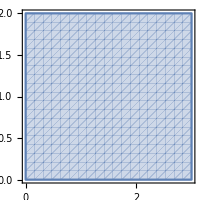

```mathematica
RegionPlot[0≤x≤3&&0≤y≤2,{x,0,3},{y,0,2},AspectRatio->Automatic]
```

Se trata de un rectángulo del plano de lados paralelos a los ejes. La variable x se mueve entre 0 y 3, mientras que la variable y se mueve entre 0 y 2.

```mathematica
∫_0^3 ∫_0^2 f[x,y]ⅆyⅆx
```

9

```mathematica
Integrate[Integrate[f[x,y],{x,0,3}],{y,0,2}]
```

9

El valor calculado es el volumen de la región en el espacio dada por la variable x entre 0 y 3, la variable y entre 0 y 2, y la variable z entre 0 y f(x,y)=xy.

El valor medio sería el correspondiente a dividir el valor obtenido (9) entre la superficie del dominio ( en este caso el rectángulo [0,3]x[0,2], por tanto 6). El valor medio es 9/6=3/2.

```mathematica
Show[{RegionPlot3D[0≤x≤3&&0≤y≤2&&0≤z≤x y,{x,0,3},{y,0,2},{z,0,6},AspectRatio->Automatic],Plot3D[3/2,{x,0,3},{y,0,2}]}]
```

-Graphics3D-

Un tipo de recinto más complejo sería el triángulo de vértices (0,0), (1,0), (0,1). En este caso, podemos considerar una cualquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se moverá entre 0 y 1-x.

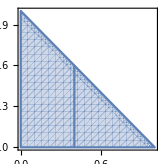

```mathematica
Show[RegionPlot[0≤x≤1&&0≤y≤1-x,{x,0,1},{y,0,1},AspectRatio->Automatic],ParametricPlot[{0.4,0.6t},{t,0,1}]]
```

La variable y se movería desde el 0 hasta el punto de la recta que une (1,0) y (0,1). Se trata de la recta x+y=1, o y=1-x.

```mathematica
∫_0^1 ∫_0^(1-x) f[x,y]ⅆyⅆx
```

1/24

```mathematica
Integrate[Integrate[f[x,y],{x,0,1-y}],{y,0,1}]
```

1/24

Un recinto más complejo es el cuadrilátero de vértices (0,0), (3,0), (4,1), (1,1).

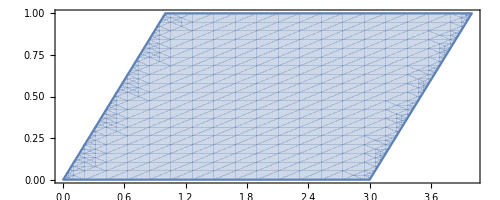

```mathematica
RegionPlot[0≤y≤1&&y≤x≤y+3,{x,0,4},{y,0,1},AspectRatio->Automatic]
```

Si decidimos considerar primero la variable x, moviéndose entre 0 y 4, nos encontramos que para ver cómo se mueve la variable y, debemos considerar tres intervalos para la x. Parece más conveniente considerar la variable y entre el 0 y el 1. Para cada valor fijado de y, estudiamos cómo se mueve la x.
Se moverá entre el recta que pasa por los puntos (0,0) y (1,1), y la recta que pasa por los puntos (3,0) y (4,1).
La primera recta es y=x, la segunda es y=x-3. Despejando x, encontramos entre qué valores se mueve.

```mathematica
∫_0^1 ∫_y^(y+3) f[x,y]ⅆxⅆy
```

13/4

Si hubiésemos considerado la variable x entre 0 y 4, habríamos tenido que calcular estas tres integrales.

```mathematica
∫_0^1 ∫_0^x f[x,y]ⅆyⅆx+∫_1^3 ∫_0^1 f[x,y]ⅆyⅆx+∫_3^4 ∫_(x-3)^1 f[x,y]ⅆyⅆx
```

13/4

Otro recinto sería el cuarto de circulo unidad centrado en el (0,0) con argumentos entre 0 y π/2 radianes.

```mathematica
RegionPlot[x^2+y^2≤ 1,{x,0,1},{y,0,1},AspectRatio->Automatic]
```

-Graphics-

Si consideramos la variable x en el intervalo [0,1], fijado x, la variable y se moverá entre 0 y el punto de la circunferencia x^2+ y^2=1. Despejando la y obtenemos, y=√(1-x^2)

```mathematica
∫_0^1 ∫_0^Sqrt[1-x^2] f[x,y]ⅆyⅆx
```

1/8

Finalmente consideremos el recinto dado por media corona circular, centrada en el punto (0,3), de radio menor 1 y radio mayor 2, con x mayor o igual que cero.

```mathematica
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,0,6},AspectRatio->Automatic]
```

-Graphics-

Este recinto podríamos estudiarlo de varias maneras.

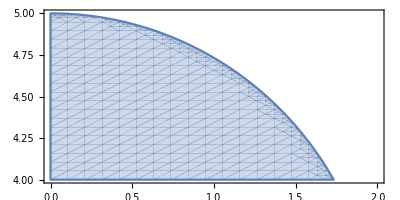
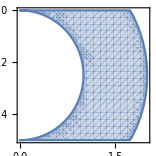
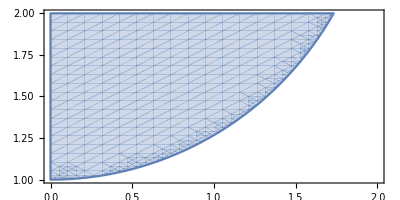

```mathematica
{RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,4,5},AspectRatio->Automatic], RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,2,4},AspectRatio->Automatic],
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,1,2},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_4^5 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy+∫_2^4 ∫_Sqrt[1^2-(y-3)^2]^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy+∫_1^2 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy
```

14

Otra forma sería,

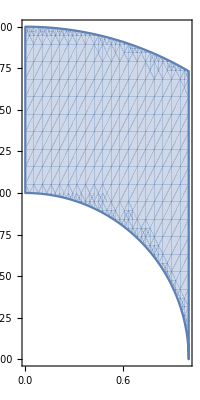
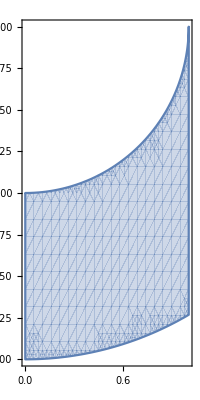
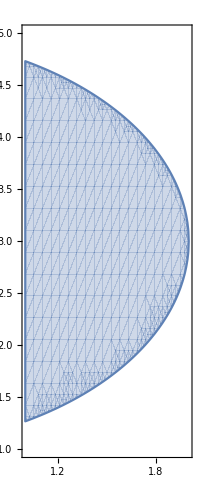

```mathematica
{RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,1},{y,3,5},AspectRatio->Automatic], RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,1},{y,1,3},AspectRatio->Automatic],
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,1,2},{y,1,5},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_0^1 ∫_(3+Sqrt[1^2-x^2])^(3+Sqrt[2^2-x^2]) f[x,y]ⅆyⅆx+∫_0^1 ∫_(3-Sqrt[2^2-x^2])^(3-Sqrt[1^2-x^2]) f[x,y]ⅆyⅆx+∫_1^2 ∫_(3-Sqrt[2^2-x^2])^(3+Sqrt[2^2-x^2]) f[x,y]ⅆyⅆx
```

14

Quizás la forma más sencilla sería considerar la integral en el medio disco grande y restarle la integral en el medio disco pequeño. Dado que la función f(x,y)=xy está definida en todo el plano, esto se podría hacer.

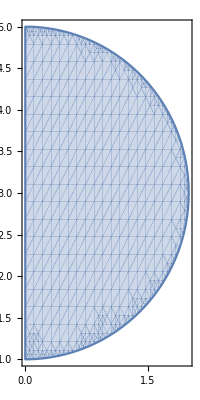
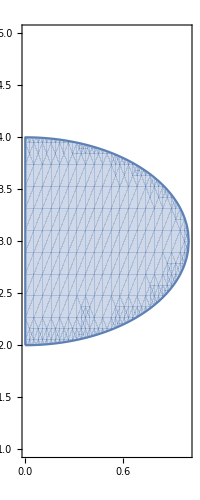

```mathematica
{RegionPlot[x^2+(y-3)^2≤ 2^2,{x,0,2},{y,1,5},AspectRatio->Automatic], RegionPlot[ x^2+(y-3)^2≤ 1^2,{x,0,1},{y,1,5},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_1^5 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy-∫_2^4 ∫_0^Sqrt[1^2-(y-3)^2] f[x,y]ⅆxⅆy
```

14

Como es lógico todos los resultados coinciden, aunque las integrales que estamos calculando pueden ser de diferente dificultad.

Para hallar los recintos y dónde se mueven cada una de las variables, tenemos que conocer la ecuación de una circunferencia si nos dan el centro (a,b) y el radio r.
(x - a)^2 + (y - b)^2=r^2
En el ejemplo anterior, teníamos dos circunferencias (la de radio 1 y la de radio 2) y para cada recinto debíamos despejar una de las variables de alguna de las ecuaciones.
Igualmente, es importante poder calcular la ecuación de una recta que pasa por dos puntos.

## MÁS EJERCICIOS • Calcular los extremos relativos de la función: ▪ f(x,y) = xy + 2/x+ 4/y ▪ f(x,y) = e^(- (x^2+ y^2 - 4y )) ▪ f(x,y) = x^2 + 4 y^2 - 2x + 8y - 1 • Calcular los extremos de la función ▪ f(x,y) =y^2 - x^2 en x^2/4+ y^2 = 1 ▪ f(x,y) = x^2 + y^2 en xy -3 = 0 ▪ f(x,y) = x^2 + 4xy + y^2 en x - y - 6 = 0 • Calcular el gradiente de f(x,y)=x^2y - x y^2 en el punto P=(-2,3). • Calcular el plano tangente a z= -10√xy en (1,-1) • Calcular el plano tangente a 2 z^2 + x^2 + y^2 = 23 en (1,2,3) • Calcular el plano tangente a z=xe^(- 2y) en (1,0,1) • Calcular el volumen de la figura limitada por arriba por la gráfica de f(x,y) = x^2 + y^2 , y en el plano por las rectas x=1, x=3, y=0, y=1. • Calcular las siguientes integrales: ▪ ∫_-1^2 ∫_3^6 10 x y^2 ⅆyⅆx ▪∫_0^1 ∫_1^3 ∫_-1^2 ( 2x +3y -z)ⅆxⅆyⅆz ▪ ∫_1^2 ∫_0^(x - 1) yⅆyⅆx ▪ ∫_-3^1 ∫_0^x 3/(x^2 + y^2)ⅆyⅆx ▪ ∫_0^2 ∫_0^(√(4 - x^2)) ( x+y)ⅆxⅆy ▪ Integral de la función f(x,y) = e^(y^2) en la región R={(x,y) / 0≤x≤2y, 0≤y≤2 }